```mathematica
Clear[d2]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
d2[n_,0]:=UnitStep[n-1]
d2[n_,k_]:=d2[n,k]=Sum[d2[Floor[n/j],k-1],{j,2,n}]
d2z[n_,z_]:=Sin[Pi z]/Pi Sum[(-1)^k/(z-k) d2[n,k],{k,0,Log2@n}]
dz[n_,z_]:=Sum[bin[z,k] d2[n,k],{k,0,Log2@n}]
d2zx[n_,z_]:=Sin[Pi z]/Pi Sum[(-1)^k/(z-k) d2x[n,k],{k,0,Log2@n}]
```

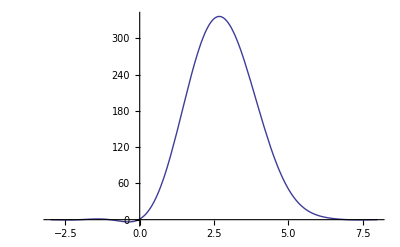

```mathematica
Plot[d2z[100,z],{z,-3,8}]
```

```mathematica
FullSimplify@Expand@d2z[100,z]
```

((720+z (18780+z (-9400+z (1947+z (-165+(-3+z) z))))) Sin[π z])/(π (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z)

```mathematica
FullSimplify@Expand@dz[100,z]
```

1/720 (720+z (1+z) (20544+z (12034+z (2861+z (194+7 z)))))

```mathematica
Expand[(720+z (18780+z (-9400+z (1947+z (-165+(-3+z) z)))))]
```

720+18780 z-9400 z^2+1947 z^3-165 z^4-3 z^5+z^6

```mathematica
roots[n_]:=If[(c=Exponent[f=bz[z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
```

```mathematica
bz[z_]:=720+18780 z-9400 z^2+1947 z^3-165 z^4-3 z^5+z^6
```

```mathematica
Sum[-1/r,{r,roots[3]}]+Sum[-1/-r,{r,1,6}]
```

28.5333+0. ⅈ

```mathematica
d2z[100,3.5593656126426385-4.024461568516174 ⅈ]
```

-2.8716×10^-11+4.17758×10^-10 ⅈ

```mathematica
roots[3]
```

{-16.4989,-0.0376246,3.55937-4.02446 ⅈ,3.55937+4.02446 ⅈ,6.20891-1.27718 ⅈ,6.20891+1.27718 ⅈ}

```mathematica
Clear[a2]
a2[n_,0]:=UnitStep[n-1]
a2[n_,k_]:=a2[n,k]=Sum[a2[n-j,k-1],{j,1,n}]
a2z[n_,z_]:=Sin[Pi z]/Pi Sum[(-1)^k/(z-k) a2[n,k],{k,0,n}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
az[n_,z_]:= Sum[bin[z,k] a2[n,k],{k,0,n}]
```

```mathematica
FullSimplify@Expand@a2z[10,z]
```

-(362880 Sin[π z])/(π (-9+z) (-8+z) (-7+z) (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z)

```mathematica
FullSimplify@Expand@az[10,z]
```

((1+z) (2+z) (3+z) (4+z) (5+z) (6+z) (7+z) (8+z) (9+z))/362880

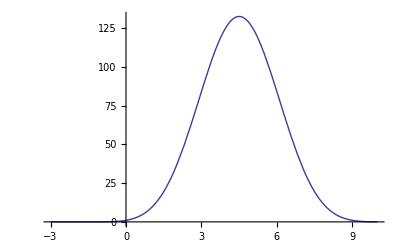

```mathematica
Plot[a2z[10,z],{z,-3,10}]
```

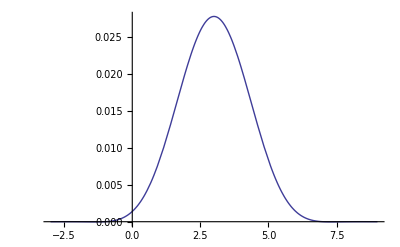

```mathematica
Plot[Sin[π z]/(π (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z),{z,-3,9}]
```

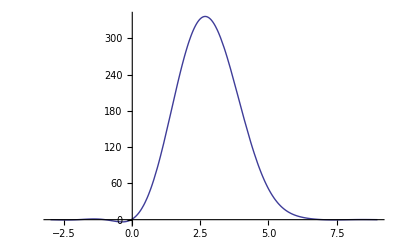

```mathematica
Plot[((720+z (18780+z (-9400+z (1947+z (-165+(-3+z) z))))) Sin[π z])/(π (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z),{z,-3,9}]
```

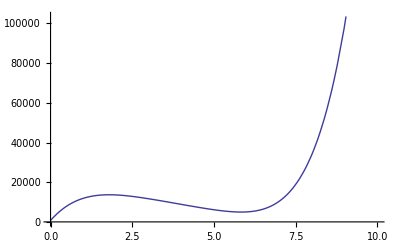

```mathematica
Plot[(720+z (18780+z (-9400+z (1947+z (-165+(-3+z) z))))),{z,0,10}]
```

```mathematica
FullSimplify@Expand@d2z[100,z]
```

((720+z (18780+z (-9400+z (1947+z (-165+(-3+z) z))))) Sin[π z])/(π (-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z)